```mathematica
data=Import["/Users/nathanhaut/Documents/GitHub/srbench-competition-2023-track-1-stackgp/datasets/dataset_2.csv"];
```

```mathematica
all=Transpose[data[[2;;]]]
```

```mathematica
input=all[[;;-2]];
response=all[[-1]];
```

```mathematica
weights=LeastSquares[Transpose[input],response]
```

{0.00515454,0.000660818,-0.0000954859,-0.0000178709,0.00054574,0.0127305,0.00163232}

```mathematica
predicted=weights.input;
```

```mathematica
Correlation[predicted,response]^2
```

0.520365

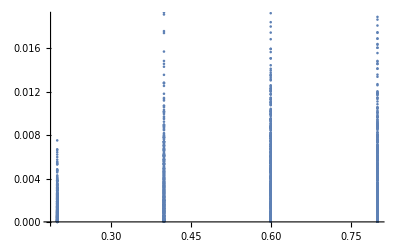
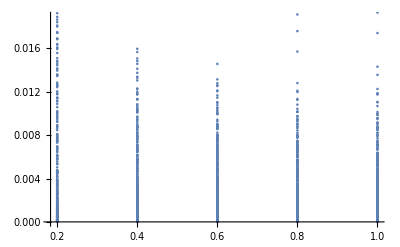
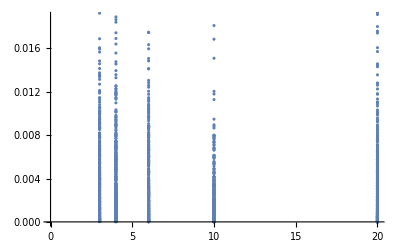
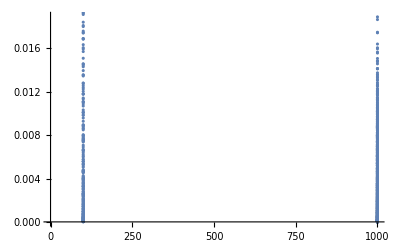
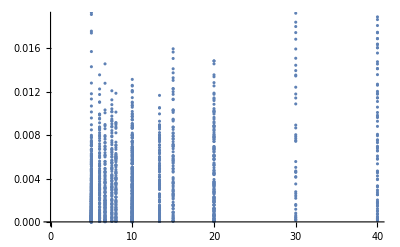
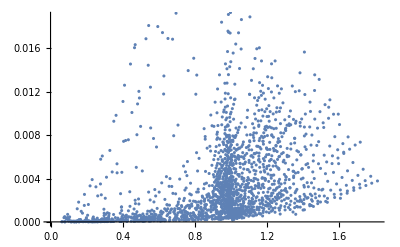
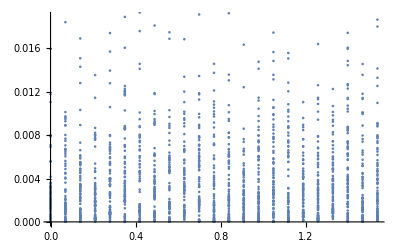

```mathematica
ListPlot[Transpose[{#,response}]]&/@input
```

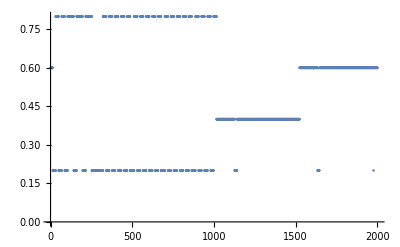
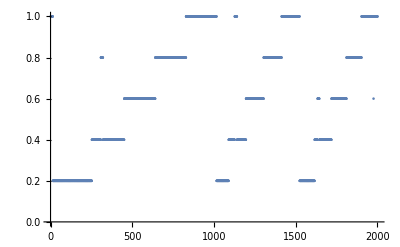
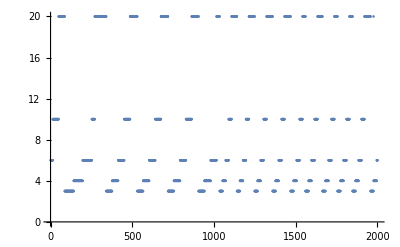
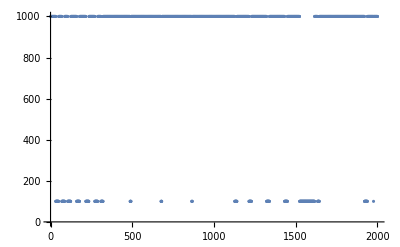
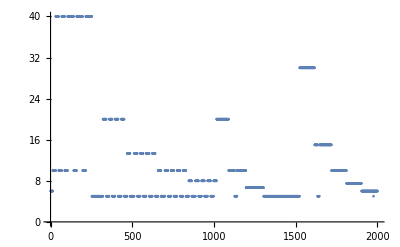
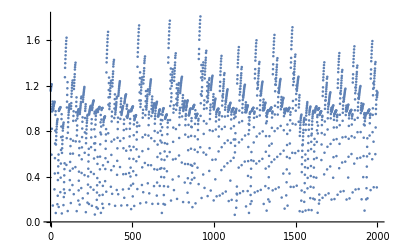
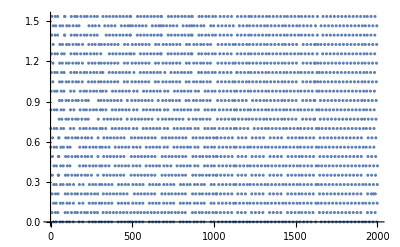

```mathematica
ListPlot[#]&/@input
```

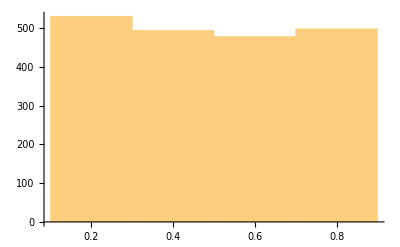
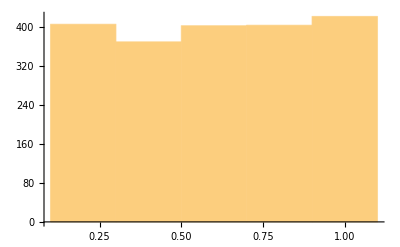
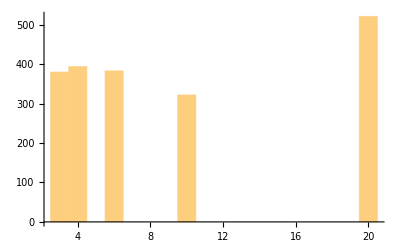
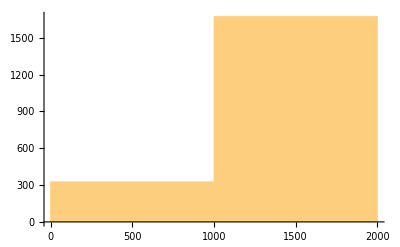
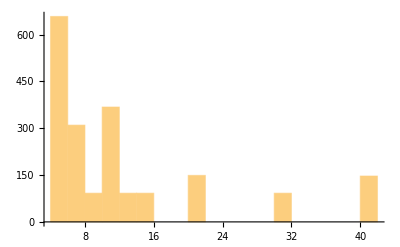
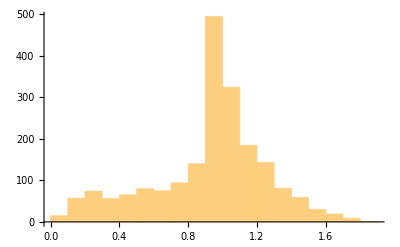
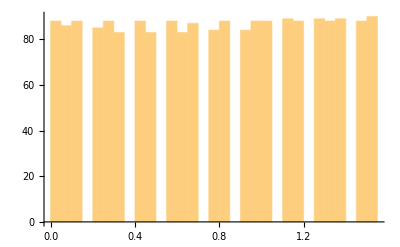

```mathematica
Histogram[#]&/@input
```

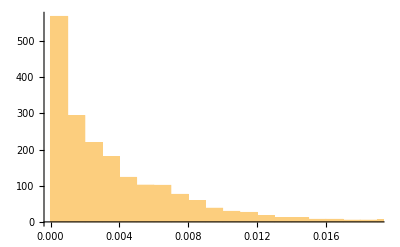

```mathematica
Histogram[response]
```

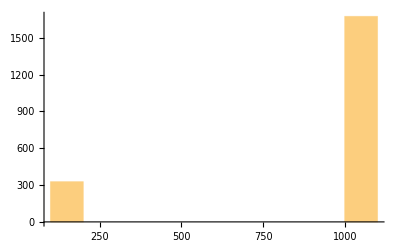

```mathematica
Histogram[Total[input]]
```

```mathematica
Length@input
```

7

```mathematica
While[True,{models=ParallelEvolve[input,response,"Ops"->allOps,"InitialModels"->ParetoFrontModels@models];,CloseKernels@Kernels[];}]
```

```mathematica
models=ParallelEvolve[input,response,"Ops"->allOps,"InitialModels"->ParetoFrontModels@models,AlignGPModels->False];
```

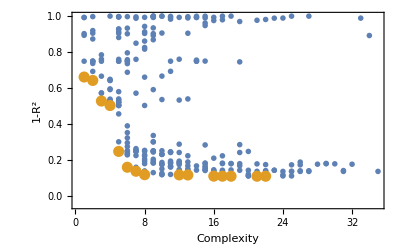

```mathematica
PlotModels[models]
```

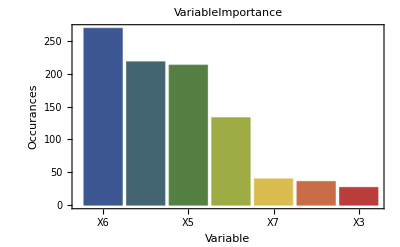

```mathematica
VariableImportancePlot[models]
```

6,4,5,1

```mathematica
Correlation[input[[1]]+input[[2]],#]&/@input
```

{0.588067,0.767989,0.00815323,0.141395,-0.200065,0.00703671,0.00640723}

```mathematica
Correlation[input[[1]],#]&/@input
```

{1.,-0.0663856,-0.117293,-0.0833306,0.553317,-0.169176,-0.00917042}

```mathematica
Correlation[input[[4]],#]&/@input
```

{-0.0833306,0.240419,-0.277146,1.,-0.445215,0.335582,-0.0359453}

```mathematica
Correlation[input[[5]],#]&/@input
```

{0.553317,-0.684959,-0.137481,-0.445215,1.,-0.237775,-0.0117701}

```mathematica
Correlation[input[[1]]+input[[4]],#]&/@input
```

{-0.0826562,0.240387,-0.277241,1.,-0.444865,0.335486,-0.0359535}

```mathematica
Correlation[input[[6]],#]&/@input
```

{-0.169176,0.142644,-0.332597,0.335582,-0.237775,1.,-0.0337603}

```mathematica
StackGPModelAccuracy[ParetoFrontModels[models][[1]],input,response]
```

0.529185

0.528436

## Reduced to inputs 1, 2, and 7

```mathematica
4->1
8->1
5->2
9->2
6->2
3->1+2
```

```mathematica
ParetoFrontModels[models][[1]]
```

StackGPModel[{X6,X2,-1,X2,2,4,X1,X7,X7,2,4,-0.104958,X2,X2,2,X2,2.71828,X1,X9,X5,X9,X3,X4,X2,X6,-2.6443×10^-12,1.,-0.143974,2.06164,0.154941},{ℵ1,ℵ1,ℵ1,ℵ1,#1 #2&,ℵ1,Log[#1]&,Inv[#1]&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,ArcCos[#1]&,ℵ1,#1^#2&,#1 #2&,#1+#2&,ℵ1,#1^#2&,Squared[#1]&,ℵ1,ℵ1,ℵ1,Sin[#1]&,Tan[#1]&,Tan[#1]&,ℵ1,#1^#2&,√#1&,√#1&,Log[#1]&,#1 #2&,#1-#2&,ℵ1,ℵ1,ℵ1,#1 #2&,Sin[#1]&,ArcSin[#1]&,#1 #2 #3 #4 #5&,ℵ1,ℵ1,ℵ1,ℵ1,ℵ1,ℵ1,ℵ1,#1+#2&,#1+#2&,#1+#2&,#1+#2&,#1 #2&,#1+#2&,#1+#2&,#1+#2&,#1+#2&,#1 #2&,#1 #2&,#1+#2&,#1 #2&,#1+#2&},{},{},{},0.528436,102,{},{X1,X2,X3,X4,X5,X6,X7,X8,X9},29]

```mathematica
PrintModel@%
```

0.154941+2.06164 (-0.143974-2.6443×10^-12 (X2+X6+X9+X5 (X2+X3+X4+X6+X9)+(1.4427-1. X2)^4 X2 (X1+X7 ArcCos[Sin[X7]]^2)^8 ArcSin[Sin[2.71828 X1]] (-0.104958-1. X2 Log[(Tan[Tan[Sin[X2]]]^2)^(1/4)])))

```mathematica
goodMod2=%
```

0.154941+2.06164 (-0.143974-2.6443×10^-12 (X2+X6+X9+X5 (X2+X3+X4+X6+X9)+(1.4427-1. X2)^4 X2 (X1+X7 ArcCos[Sin[X7]]^2)^8 ArcSin[Sin[2.71828 X1]] (-0.104958-1. X2 Log[(Tan[Tan[Sin[X2]]]^2)^(1/4)])))

```mathematica
goodMod2/.{"X4"->"X1","X8"->"X1","X5"->"X2","X6"->"X2","X9"->"X2"}
```

0.154941+2.06164 (-0.143974-2.6443×10^-12 (3 X2+X2 (X1+3 X2+X3)+(1.4427-1. X2)^4 X2 (X1+X7 ArcCos[Sin[X7]]^2)^8 ArcSin[Sin[2.71828 X1]] (-0.104958-1. X2 Log[(Tan[Tan[Sin[X2]]]^2)^(1/4)])))

```mathematica
0.15494073597976038+2.0616408491936027 (-0.14397407138233212-2.6442987147481578*^-12 (3 "X2"+"X2" ("X1"+3 "X2"+"X3")+(1.4426950408889634-1. "X2")^4 "X2" ("X1"+"X7" ArcCos[Sin["X7"]]^2)^8 ArcSin[Sin[2.71828182845905 "X1"]] (-0.10495768705324338-1. "X2" Log[(Tan[Tan[Sin["X2"]]]^2)^(1/4)])))/.{"X1"->input[[1]],"X2"->input[[2]],"X7"->input[[7]],"X3"->(input[[1]]+input[[2]])}
```

{-0.114731,-0.141808,-0.143011,-0.141581,-0.150872,-0.141882,-0.141882,-0.141882,-0.141882,-0.0324175,-0.141882,-0.141374,1.87904,-0.141882,-0.141882,-0.13436,-0.141882,-0.140623,-0.141882,-0.141854,-0.141863,0.206329,-5.67193,-0.141882,-0.141731,-0.141861,-0.141882,-0.141992,-0.141882,-0.141882,-0.141882,-0.756901,-0.141882,-0.112926,5.90023,0.0832543,-0.138702,-0.14191,3.30123,-0.142269,-0.142301,-0.271926,-0.141882,-0.141389,-0.141882,-0.141815,-0.141884,0.929243,-0.155477,0.912629,-0.141882,-0.141869,-2.03579,-0.141862,-0.141882,-0.141882,-0.0599087,-0.141854,-0.141364,-0.0521349,-0.14186,-0.141938,1.4913,-0.141982,-0.141885,-0.0390491,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.142857,-0.141882,-0.141882,-0.141813,-0.141872,-0.141882,-0.142198,-0.152883,-0.137335,-0.177945,-0.169383,-0.143539,-0.142044,-0.141882,-1.57998,-0.111748,-0.141875,-0.141882,-0.107538,0.456625,-0.514388,-0.141883,-0.134633,-0.141882,-0.143269,-2.0663,-0.141882,-0.141882,-0.14397,1.16534,-0.142242,-0.141882,-0.141882,-0.143751,-0.175627,-0.141882,-0.145931,-0.141882,-0.19286,-0.141882,-0.299354,-0.146515,-0.141883,-0.141883,-0.190814,-0.141882,-0.148556,-0.141882,-0.141879,-0.141882,-6.2077,-3.45104,-0.141789,-0.141882,-0.141882,-0.141876,-0.142596,-0.141958,-0.0701271,-0.141882,4.00577,-0.141882,-0.140638,-0.141757,-0.141882,-0.141884,-0.14191,-0.141882,-0.141883,-0.797919,-0.141882,0.387723,-0.141882,-0.141882,-0.141882,-0.141875,-0.160093,-0.0849096,-1.64378,-0.141882,-0.138781,-0.181173,-0.141883,-0.141882,-0.142559,-3.34123,-0.141882,-0.141929,-0.141882,-0.141864,-0.141883,-0.141882,-0.141896,-0.198716,4.77808,-0.140768,-0.141882,-0.0806181,-0.14184,-0.141882,-0.186956,-0.141882,-0.405571,-0.141882,-0.141834,-0.141882,-0.134048,1.08811,-0.141882,-0.141882,-0.141882,-0.141882,-0.14192,0.378295,-0.141882,-0.141882,4.80594,-0.141882,-0.142473,-0.141893,-0.141882,-0.141882,-0.142085,-0.141867,-0.141877,-0.141871,-0.141882,-0.141831,-0.141913,-0.143173,-0.141176,-0.141885,-0.0848022,-0.180014,-0.0105002,-0.117235,-0.140382,-0.141883,-0.141882,-0.140123,-5.23949,-0.141838,-0.132597,-0.0956277,-0.141881,-0.140226,-0.141882,-0.140492,-0.141882,-0.141895,-0.141882,-0.141882,-0.141882,-0.143821,-0.141882,-0.141882,-0.141877,-0.141892,-0.141742,-0.678541,-0.147588,-0.141882,-0.141817,-0.142493,-0.140526,-0.141883,-0.141882,-0.151701,-0.141075,-0.141882,-1.16717,-0.141882,-0.141882,-0.141882,-0.141862,-0.14242,-0.141884,-0.141882,-0.139202,-0.14194,-0.141882,-0.139612,-0.225914,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.14208,-0.141882,-0.161387,-0.63335,-0.141882,-0.141882,-0.141864,-0.141882,-0.14188,-0.141492,-0.141882,0.0606454,-0.13981,-0.144643,-0.141882,-0.141882,-0.141882,-0.141882,-0.141647,-0.225468,-0.141836,-0.140812,-0.142019,-0.141884,-0.141882,-0.141882,-0.141881,-0.141882,-0.141882,-0.142416,-0.141882,-0.141882,-0.141882,-0.102052,-0.141882,-0.142105,-0.141882,-0.141882,0.0259978,-0.141882,-0.141905,-0.544409,-0.141883,-0.14188,1.62078,-0.141882,-0.141808,-0.141882,-0.141517,-0.141882,-0.141884,-0.161258,-0.141882,-0.141443,-0.141882,-0.141882,-0.137238,-0.141421,-0.0880016,-0.141866,-0.142501,-0.141882,-0.141258,0.582143,-0.135407,-0.141939,7.69364,-0.141882,-0.14188,-0.141882,-0.141884,-0.141882,0.112517,4.51026,-0.141882,-0.141882,-1.5235,-0.0958177,-0.142835,-0.141697,-0.142505,-0.141882,-0.141896,-0.141882,-0.141882,-0.141882,-0.142072,-0.141886,-0.137438,1.03093,-0.141886,-0.141837,0.657544,-0.141882,-0.141882,-0.141884,4.58226,-0.141887,-0.141883,-0.141882,-0.273871,-0.141882,-0.142093,-0.148902,-0.141866,-0.141882,-0.141885,-0.142806,-0.128608,19.6697,-0.141882,-0.141881,-0.141882,-0.12084,-0.141882,-0.141882,-0.952457,-0.141882,-0.141861,6.03446,-0.141882,19.952,-0.141818,-0.141954,1.00724,-0.141882,-0.141882,-0.141883,-0.141882,-0.141882,14.856,0.986353,-0.140118,-0.141882,-0.141879,-3.42169,-0.141882,-0.141885,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141892,-0.1441,0.00244757,-0.141882,-0.141835,-0.141882,-0.799656,-0.141882,-0.136102,-0.14188,0.204776,-0.141876,-0.141917,-0.0312296,-0.141882,-3.63035,-0.141782,-0.141871,-0.141882,-0.141882,-0.141882,-0.141882,-1.19106,-0.141887,-0.141882,-0.141882,-0.142447,-0.437711,-0.141882,15.0968,-0.141882,-0.141899,-0.141882,-0.141617,-0.382285,-0.144951,-0.216419,-0.141882,-0.141882,-0.141882,-0.141882,-0.0364988,-0.141882,-0.141878,-0.141311,-0.141882,-0.142966,-0.132805,-0.141881,-0.141769,-0.141882,-0.141882,-0.141885,-0.141882,-0.135138,-0.0769172,-0.141882,-0.144912,-0.141884,-0.141882,-0.139297,-0.141882,-0.1422,-0.141693,-0.141872,-0.141882,-0.142242,-0.141882,-0.154325,-0.141882,-0.143546,-0.141948,-0.141882,-0.141882,0.530237,-0.14001,-0.141882,-0.141882,-0.142188,-0.141882,-0.144597,-0.172755,-0.141853,-0.175894,-0.141837,-0.144688,-0.159379,0.526532,-0.141787,-0.140957,-0.141882,0.118983,2.19062,-0.141882,-0.141882,-0.141846,-0.814682,-0.141837,-0.146074,-0.139474,-0.141882,2.13075,-0.800292,-0.108987,-0.141882,-0.141882,-0.141814,-0.141882,-0.967577,-0.141882,-0.638342,-0.141918,-0.122992,-0.141882,-0.141899,-0.153684,-0.141882,-0.141882,-0.141881,21.7391,-0.141844,-0.141882,-0.141903,-0.141845,-0.141878,-0.141882,2.50393,-0.141916,-0.141882,0.623443,-0.141882,-0.141882,0.548859,-0.141882,-0.141882,-0.141882,20.4797,-0.141875,-0.141882,-0.141882,-0.140628,-0.141882,-0.141883,-0.130362,-0.10412,-0.141882,-0.141884,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.142284,-0.141887,-0.141882,2.8335,-0.14266,0.323171,-0.141885,-0.141882,-0.141881,-0.141781,-0.141882,-0.141882,-0.141906,-0.125236,-0.14188,-0.141884,4.65365,-0.141879,-0.141882,-0.141883,-0.141868,-0.141883,-0.141882,-0.129103,-0.141882,-0.141882,-0.141882,-0.141882,18.3464,-0.141882,-0.141882,-0.44394,1.26135,0.0933014,5.83572,-0.141882,-0.127448,-0.141882,-0.141887,-0.141859,-0.141871,-0.141882,-6.35783,1.97852,-0.141048,-0.141882,-0.141882,-0.141588,-0.142809,-0.141882,-0.141882,0.445711,-0.323156,-0.141852,0.0496919,-0.141882,-0.141882,-0.141882,-0.141883,-0.141882,-0.141882,-0.208412,-0.141882,-0.141882,-0.141879,-0.141882,5.27329,-0.141882,-0.141882,-0.141882,-0.141327,-0.141882,-0.141882,-0.141882,-0.141882,-1.31822,-0.141882,-0.141882,-0.141882,-0.141882,-0.141883,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,0.145323,-0.141882,-0.141882,-0.141864,13.1807,-0.740432,-0.141882,-0.693798,-0.141853,-1.37158,-0.156691,-0.142328,-0.139867,-0.142114,-0.141882,-0.141882,-0.141882,-0.141882,-0.150152,-0.141882,-0.141882,-0.144583,-0.141911,-0.141882,-0.141593,-0.141883,-0.141882,-0.260892,-3.33981,-0.141882,-0.143008,-0.141882,-0.220071,18.8739,-0.141881,-0.14165,-0.132067,18.353,-0.221873,-0.142242,-0.141882,-0.14189,-0.141882,8.80691,0.19085,-0.14217,-0.142079,-0.869886,-0.141773,-0.141885,-0.141882,6.33888,-0.284239,-0.141824,-0.143406,-0.172776,-0.141882,-0.141882,10.5041,-0.147672,-0.141882,-0.141797,-0.141882,-0.141882,-0.23064,-0.141882,-3.06096,-0.141882,-0.141883,-0.141882,-0.141894,-0.14036,-0.141882,-0.141882,-0.142283,-0.141882,-0.141882,0.770098,-0.141808,-0.137198,-0.141876,-0.141882,-0.233699,-0.141882,-0.141882,-0.142416,-0.141882,-0.142035,-0.141948,-0.141906,-0.142074,0.0216088,-0.141882,-0.382471,-0.141882,-0.141882,-0.141879,-0.141882,-0.153352,-0.141882,-0.138146,-0.225823,-0.140225,-0.141874,-0.141853,-0.141882,-0.141882,-0.173719,-0.141447,-0.12295,-0.141883,-0.141883,-0.141669,-0.141882,-0.141882,-0.139673,-0.141882,-0.391333,-0.141858,0.0517391,-0.141867,-0.141882,-0.141882,-0.142384,-0.14187,-0.627187,-2.7119,-0.141883,-0.141882,-0.141882,-0.13243,20.3252,-0.141941,-0.141882,-0.141882,-0.141884,-0.134968,-0.141882,-0.141356,-0.141882,-0.141878,-0.141882,-0.141882,-0.141882,-0.142027,-0.141882,-0.141882,-0.141882,-0.141997,-0.142498,-0.141882,0.473374,-0.26307,-0.141854,-0.133031,-0.141887,-0.141882,-0.144699,-0.141882,-0.141882,-0.141882,-0.141881,-0.141882,-0.141878,5.21742,-0.141882,-0.143755,-0.141882,-0.142218,-0.141882,-0.1425,-0.141882,-0.141882,-0.141882,-0.14186,-1.86224,-0.14188,-0.131425,-0.141882,-0.141882,-0.138725,-0.141882,-0.141882,-0.141882,-0.1406,-0.12614,1.62045,-0.141882,-2.47489,-0.141882,3.15257,-0.141881,-0.602021,-0.141882,-0.141882,-0.141894,-0.141894,-0.136404,-0.141882,-0.141882,-0.141882,6.24737,-0.140496,0.170024,0.0996578,-0.141883,-0.141882,-0.142255,6.81514,-0.141884,-0.141875,-0.141883,-0.141882,-0.141882,-0.141882,-0.142162,-0.141882,-0.123518,-0.141881,-0.141882,1.2258,-0.141884,-0.141882,-0.164169,-0.141882,-0.16097,-0.141882,-0.200801,-0.141882,-0.141882,-0.141882,-0.141882,-0.141884,-0.212763,-0.14188,12.1206,-0.141882,-0.141882,-0.861451,-0.141878,-0.141868,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,0.637131,6.92038,-0.141882,-0.141527,-0.141886,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141895,1.47879,-0.141882,-0.31148,-0.155211,-0.141855,-0.114645,-0.141882,-0.142296,-7.20937,-0.141882,-0.141882,-0.141882,-0.141871,-0.141882,-0.141882,-0.141882,-0.142332,-0.141882,0.921333,-0.141891,-0.141895,-0.244892,0.696638,-0.176691,-0.141882,-0.141878,-0.141765,-0.0631985,-0.127275,-0.14455,-0.508286,-0.141882,-0.141882,-0.141886,-0.109548,-0.141458,-0.141882,-0.141882,-0.143475,-0.112129,-0.0971681,-0.141881,14.4806,-0.141882,-0.141882,-0.141882,-0.142709,-0.141882,-0.321781,-0.141432,-0.141882,-0.138274,-0.141885,-0.142103,-0.14189,-0.144751,-0.147787,-0.141882,-0.142205,-0.142288,-0.141882,-0.141882,-0.141882,-0.141882,-0.14182,-0.141879,-0.141881,-0.141908,-0.140073,-0.140803,-0.141882,-0.141882,-0.141882,-0.141882,-0.69793,-0.141882,-0.141882,-0.141882,-0.141887,-0.141882,0.0412575,-0.15102,-0.141882,-0.141882,-0.141882,-0.141882,-0.141892,-0.888285,-0.141882,-0.141882,-0.141882,-0.142544,-2.97277,-0.141882,-0.80167,-0.141881,-0.142636,-0.14371,-0.138774,-0.142086,-0.141882,-3.894,-0.185036,-0.141878,-0.141882,-0.141403,5.13349,-0.141847,-0.141882,-0.145171,-2.56027,-0.141878,-0.141882,-0.141877,-0.141882,-0.142244,-0.142133,-1.13673,-0.141882,-0.179506,-0.141882,-0.141882,-0.1365,-0.142045,-0.141849,-0.141864,-0.141882,-0.125243,-0.141879,-0.141882,-0.14183,-0.550685,12.3511,-0.141882,-0.141682,-0.141882,-0.273365,-0.146595,-0.141937,-0.132156,-0.141871,-0.141879,-0.141882,-0.141768,-0.141882,-0.141882,0.773034,-0.538245,-0.141882,-0.141882,-0.141878,-0.141827,-0.141895,-0.141882,-0.148784,-0.141882,-0.141882,-0.141882,-0.141854,-0.147939,-0.141882,-0.141882,-0.141882,-0.142605,-0.0669949,-0.114587,-0.110288,-0.141879,2.06495,-0.141874,-0.141985,-0.141882,-1.58292,-0.141733,-0.14172,-0.141881,1.43591,-0.141882,-0.141882,-0.141882,-0.115132,-0.545263,-0.141941,-0.134591,0.104917,-0.141882,-0.141893,-0.141882,-0.141889,-0.141882,-0.141882,-0.141882,-2.13813,-0.136414,-0.142641,-0.141882,-0.141882,-0.141882,-0.141882,-4.59206,-0.141882,-0.141882,0.111886,-1.43315,-0.141882,-0.184821,-0.141882,-0.141369,-0.0882145,1.57636,-0.141882,-0.141882,-0.141882,-0.399048,-0.141882,-0.141882,-0.141898,-0.141274,-0.141881,-0.141882,-0.141902,0.0913645,-0.141886,-0.0962225,-0.132802,-0.141881,-0.141882,-0.141882,-0.629879,-0.140875,0.0695027,-0.141883,-0.141882,-0.142334,-9.51006,0.339926,-0.141882,-0.141882,0.358508,0.127977,-0.141909,-0.141882,-0.1419,-0.141881,-0.141882,0.724128,-0.141882,-0.141882,-1.03675,-0.141882,-0.141834,-0.141882,-0.141882,-0.139513,-0.141883,-0.141882,-0.0103924,-0.127918,-0.141882,-0.141882,-0.141883,-0.141882,-1.80982,-0.131713,-0.141881,-0.0930262,-0.142126,-0.141882,-0.141415,-0.144005,-0.141878,-0.14188,-0.141723,-0.141859,-0.180341,-0.141882,0.201791,-0.142072,-0.141882,-0.141882,-0.141882,-0.406143,-0.141882,-0.141883,-0.143374,-0.141884,-0.141907,-0.575067,-0.101445,-0.141739,-3.10103,-0.141882,-0.141882,-0.141882,-0.141882,-0.14094,-0.141883,-0.141315,-0.141892,10.1497,1.2733,-0.141882,-0.141882,-0.141882,-0.141881,-0.158013,-0.145821,-0.141874,-0.141902,-0.141882,0.160262,-0.141889,-0.163779,-0.141882,-0.141882,-0.141892,-0.141962,-0.141882,-0.141882,-0.141882,-0.142462,-1.6489,-0.148067,-1.96196,-0.141882,-0.133078,-0.111368,-0.141882,-1.92141,-0.141882,-1.06732,-0.141871,-0.141882,-0.141884,-0.141757,-0.141882,-0.141882,-0.141882,-0.14188,-0.141882,0.0609941,-0.141882,-0.141883,-0.141881,-0.141882,-0.161659,-0.141883,-0.115376,-0.141846,-0.141882,-0.142271,-0.14195,-0.141882,-0.141882,-0.141896,-0.141883,-0.141882,2.63445,-0.141882,-0.141882,-0.141639,-0.0305561,-0.141888,-0.127472,-0.141878,-0.269729,-0.142966,-0.141872,-0.142221,-0.137019,-0.138203,-0.141882,1.59494,-0.1382,-0.141882,-0.141882,0.516525,-0.141882,-0.142761,-7.22151,-0.142109,-0.141882,-0.141998,0.072687,-0.141883,-0.141882,-0.141847,-0.285576,-0.141882,-0.141877,-0.141903,-0.117331,-0.141882,0.272571,-0.670104,-0.141882,-0.141854,-0.141883,-0.141881,0.388785,-0.141895,15.0921,-2.6738,-0.141868,-0.141857,-0.141235,-0.141882,-0.140213,-0.141882,-0.146068,-0.141882,-0.141882,-0.14188,-0.139147,-0.141882,-0.141882,0.039699,-0.141882,-0.141882,-0.141882,-0.141882,-0.131385,-0.141882,-0.141882,-0.142401,-0.141882,-0.141882,-0.141766,-0.141882,-0.141882,-2.63329,-0.14189,-0.141788,-0.141882,-4.95868,-0.141882,-0.141882,-0.141882,-0.14187,-0.161241,-0.141867,-0.675581,-0.141882,-0.141882,-0.141882,-0.141242,-0.141882,-0.141882,-0.141882,0.118817,-0.131616,0.200182,-0.141882,0.569616,-0.141882,-0.141884,-0.141882,-0.141882,-0.141874,-0.139809,-2.05482,-0.146029,-0.141885,-1.0067,-0.141882,-0.141882,-0.139829,-0.141781,-0.141272,-0.143127,-0.141882,-1.90026,-0.141882,-0.141882,-0.143175,-0.941967,-0.131657,-0.141845,-1.00825,-0.141867,-0.141882,-0.141882,-0.141882,-0.143095,-0.141882,-0.141884,-0.144034,-5.13585,-0.141854,-1.40695,-0.141856,-0.141882,-0.14188,-0.141882,-0.141882,-0.156272,-0.141882,-0.141882,-0.192895,-0.141882,-0.148599,-0.141905,-0.141882,-0.141996,0.542419,-0.171512,-0.141879,-0.141882,-0.141882,4.46918,-0.141882,-0.170759,-0.193255,-0.141882,-0.141856,-0.141882,-0.141882,-0.141854,5.18273,-0.141885,-0.141548,-0.141882,-0.141798,-0.141882,-0.141882,-0.848895,-0.141882,-0.141649,-0.137463,-0.141882,-0.118543,-0.135512,-0.141882,-0.141488,-0.141883,-0.141882,-0.144111,1.33215,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.210108,-0.141882,-2.83566,-0.141882,-0.135839,-0.141844,-0.141883,-0.141882,-0.128456,-0.141882,-0.14763,-0.141882,0.128017,-0.690387,-0.196933,-0.489049,-0.141882,-0.141882,-0.258964,-0.141878,-0.141835,-0.0557732,-0.141882,-0.141882,-0.141882,-0.142187,-0.141882,-0.141882,-0.141889,-0.141882,-0.14204,-0.141882,-0.141906,-0.141882,-0.140693,-0.141882,-0.141882,-0.141882,0.156732,-0.141882,-0.141882,-0.141882,-0.141883,-0.144816,-0.141882,-0.140468,-0.141882,-0.140776,-0.141881,-0.141906,-0.141882,-0.141882,-0.141882,6.14152,-2.97013,-0.141882,-0.21631,-0.142761,-0.794937,-0.141882,-0.141883,-0.141882,-0.141882,-0.251544,-0.141882,-0.146675,-0.139186,-0.147627,-0.141882,-0.0990457,-0.141882,-0.142156,-0.141864,-0.141882,-0.167439,0.174897,-0.141882,-0.141882,-0.141882,-0.141882,-0.150752,-0.141882,-0.141882,-0.1419,-0.141515,-0.141882,-0.141883,-4.6413,-0.141882,-3.1222,-0.141882,-0.141828,-0.138771,-0.141882,-0.141882,-0.141882,-0.143351,-0.233388,0.080756,-1.46002,-0.141882,-0.141882,-0.223623,-0.142378,-0.141882,1.24722,-0.141882,-0.116977,-0.146255,1.2627,-0.141882,0.0178671,-0.233838,-0.142894,-0.141971,-0.141871,0.478227,-0.141882,-0.144371,0.22197,-0.141882,-0.141888,-0.141882,-0.162251,-0.14094,-0.143963,-0.141882,-0.141882,-0.141882,-0.142164,-0.141882,-0.142519,0.531085,-0.141882,-0.141882,-0.141838,-0.141366,-0.141877,-0.141883,-0.141883,-0.141882,-0.141876,-0.14398,-0.141882,-0.143884,0.299313,-0.141882,-0.141845,-0.141928,-0.141882,-0.141751,-0.141882,-0.141882,0.0458077,-0.142112,-0.144413,-0.141821,0.00391634,-0.141882,-0.141882,-0.141882,-0.141829,-0.12033,-0.141893,-0.141898,5.36063,-1.28683,-0.141882,-0.141888,-0.141882,4.73773,-0.140442,0.735681,-0.141717,-0.141882,-0.141879,-0.122892,0.546038,-0.141882,-0.141882,-0.141882,-0.136983,-0.189497,-0.13703,-0.141882,-0.141882,-0.141882,-0.141882,-0.14304,-0.141882,-1.64009,-0.119814,-0.141767,-0.139218,-0.110562,-0.141876,-0.141882,-0.162804,-0.141882,-0.141894,-0.141868,-0.141542,-0.141882,-0.141882,-0.140773,-0.141882,-0.141882,-0.141882,-0.169766,-0.141882,-0.141882,-0.141883,-0.142005,-0.141882,-0.141882,-0.141882,-0.141882,-0.136394,-0.141879,-0.141879,-0.142468,-0.161283,0.469524,-0.138353,-0.141882,12.2778,-0.141882,-0.143043,4.75872,0.75319,-0.141928,-0.0897834,-0.142233,-0.141882,-0.141882,-0.141883,-0.141861,-0.211953,-0.141882,-0.141797,-0.141882,-0.14188,0.529334,-0.0556418,-0.141882,-0.14377,-0.1419,-0.141854,-0.141432,-0.145747,1.00666,-0.141882,-0.141874,-0.122356,-0.141684,-0.254127,-0.201256,-0.130284,-0.209007,-1.0382,-0.142306,-0.141884,-0.172715,-0.141882,-0.141815,-0.141882,-0.140786,0.133697,-0.141882,-0.141882,-0.141882,-0.141882,-0.14188,-0.143492,-0.140124,-0.141882,-0.14185,-0.141882,-5.19957,-0.142613,-0.141921,-0.141882,-0.141882,-0.141884,-0.141882,-0.141436,-0.141882,-0.141806,-0.141724,-0.143448,-0.141855,-0.497715,-0.141882,-0.141828,-0.399516,-0.141882,-0.141937,0.272376,-0.141882,1.85569,-0.1388,-0.139292,-0.141882,-0.141855,-0.141882,-0.141882,-0.142545,-0.141882,-4.27787,-0.141878,-0.141882,-0.141882,-0.14188,-0.141881,-0.0970314,-0.141882,-0.141905,-0.141882,-0.141882,-0.141889,-0.141882,-0.246386,-1.87235,-0.141879,-0.141882,-0.141862,-0.141747,-0.141882,-0.139982,-0.141882,0.412385,-0.141882,-0.141882,-0.141882,-0.142185,-0.141889,-0.141894,-0.141889,-0.114704,-0.141882,-0.141859,-0.135145,-0.141884,-0.141882,-0.141882,-0.14545,-0.141876,-0.141882,-0.122872,11.5274,-0.141882,-0.152919,-0.141882,-0.150703,-0.144733,-0.141881,-0.141882,-0.138668,-0.141866,-0.141908,-0.141922,-0.141882,-0.0498693,-0.141882,-0.141882,-0.142463,-0.141863,-0.141882,-0.0432183,2.09414,-0.141882,-0.119926,-0.141882,-0.141882,-0.141882,-0.141884,-0.143003,-0.143188,8.19424,-0.141882,-0.141882,-0.139508,-0.0299404,-0.141637,-0.141881,-0.141882,-0.141882,-0.14188,-0.141882,-0.141882,-0.141882,-0.141882,-0.141882,-0.134265,-0.0964028,0.424653,-0.141882,-0.141882,-0.141882,-0.141882,-0.141879,-0.141882,-0.141903,-0.141859,-0.144249,-0.141887,-0.141899,-0.141882,-0.141882,0.426774,-0.142022,-0.141882,-0.14575,-0.141882,18.237,-0.141957,-0.141883,-0.141882,15.1946,-0.141882,-0.141882,-0.141882,-0.141882,-0.142173,-0.142343,-0.139924,0.04018,-0.14189,-0.141882,-0.142117,-1.76855,-0.141882,0.445195,-0.141882,-0.141099,-0.141887,-0.141882,-1.58124,-0.141882,-0.142216,-0.141863,-0.141888,-0.141866,-0.327356,-0.141882,-0.141882,-0.141887,-0.141882,-0.141848,-0.143031,-0.141882,-0.141882,-0.141895,2.62196,-0.141882,-0.142093,-0.14209,-0.327841,-0.141881,-0.141882,-0.0579356,-0.126184,-0.213075,-0.141882,-0.141882,-0.141882,-0.141881,-0.141882,-0.141882,-0.134267,-0.416419,-0.0394964,-0.140953,-0.138585,-0.141882,-2.15734,-0.141874,-0.141879,8.56162,-0.141881,-0.141883,-0.146927,-0.142715,-0.343173,-0.151515,-0.141882,-0.141882,-0.141882,1.24699,-0.141873,-0.141882,0.568817,22.6087,-0.14193,-0.141879,-1.69671,0.00483725,-0.141882,-0.123779,-0.970013,-0.065603,-0.333841,-0.141882,-0.141882,-0.141882,-0.664671,-0.14322,-0.141092,0.344962,-0.141893,-0.14188,-0.135351,-0.141882,-0.141882,-0.303313,-0.142651,-0.141882,-0.141882,-0.132061,-0.141882,7.93523,-0.141882,0.23912,-0.141882,-0.141882,-0.141882,1.61915,-0.141882,-0.141882,-0.136278,-0.141882,-0.141882,-0.14183,-0.141898,-0.0914323,-0.141882,-0.141882,-0.141882,-0.141882,-0.339048,-0.517408,4.14578,-3.55844,-0.141882,-0.480405,-0.141882,-0.141881,-0.133199,-0.0658624,-0.141882,-0.127458,-0.141877,-0.141882}

```mathematica
Correlation[%,response]^2
```

0.471564

```mathematica
Correlation[EvaluateGPModel[ParetoFrontModels[models][[1]],input],response]^2
```

0.471564

```mathematica
reducedInput=input[[{1,2,4,6}]];
```

```mathematica
modelsR={};
```

```mathematica
modelsR=ParallelEvolve[reducedInput,response,"Ops"->allOps,AlignGPModels->False,"InitialModels"->ParetoFrontModels@modelsR,"NumberOfModels"->300,"Generations"->300];
```

What if we made meta-variables of simple models on ParetoFront to see if they boost performance. Or minimize constants to make a linear combination of ParetoFront models.

Maximize correlation of linear combination: Max[correlation[a*fx1+b*fx2...]]

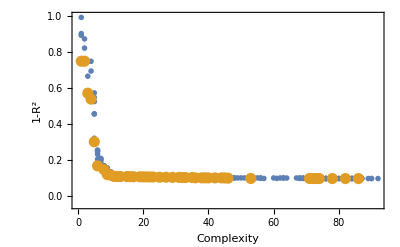

```mathematica
PlotModels[modelsR]
```

```mathematica
modelsR
```

```mathematica
StackGPModelAccuracy[ParetoFrontModels[modelsR][[1]],reducedInput,response]
```

0.0966225

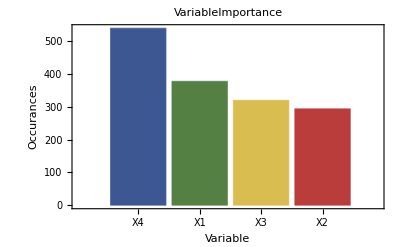

```mathematica
VariableImportancePlot[modelsR]
```

```mathematica
Length@ParetoFrontModels@modelsR
```

43

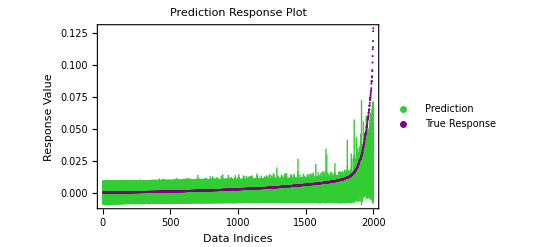

```mathematica
PredictionResponsePlot[EnsembleSelect[modelsR,reducedInput,response],reducedInput,response]
```

```mathematica
NMaximize[Correlation[a*EvaluateGPModel[ParetoFrontModels[modelsR][[1]],reducedInput]+b*EvaluateGPModel[ParetoFrontModels[modelsR][[-2]],reducedInput]+c*EvaluateGPModel[ParetoFrontModels[modelsR][[-3]],reducedInput]+d*EvaluateGPModel[ParetoFrontModels[modelsR][[-4]],reducedInput]+e*EvaluateGPModel[ParetoFrontModels[modelsR][[-4]],reducedInput]+f*EvaluateGPModel[ParetoFrontModels[modelsR][[-6]],reducedInput]+g*EvaluateGPModel[ParetoFrontModels[modelsR][[-7]],reducedInput]+
h*EvaluateGPModel[ParetoFrontModels[modelsR][[-8]],reducedInput]+
j*EvaluateGPModel[ParetoFrontModels[modelsR][[-9]],reducedInput]+
k*EvaluateGPModel[ParetoFrontModels[modelsR][[-10]],reducedInput]+
l*EvaluateGPModel[ParetoFrontModels[modelsR][[-11]],reducedInput],response]^2,{a,b,c,d,e,f,g,h,j,k,l}]
```

{0.908429,{a→-0.684529,b→0.0727828,c→-0.13044,d→0.240948,e→-0.0643692,f→-1.66304,g→-3.85424,h→-3.55487,j→7.66752,k→7.1221,l→-0.0167864}}

## Cross-modelling analysis

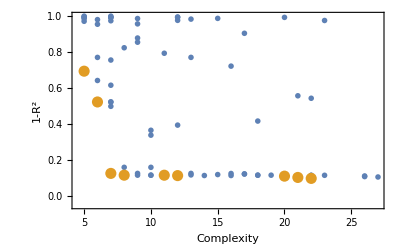

```mathematica
i=1;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

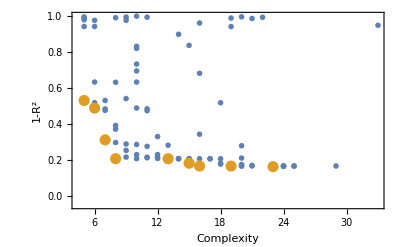

```mathematica
i=2;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

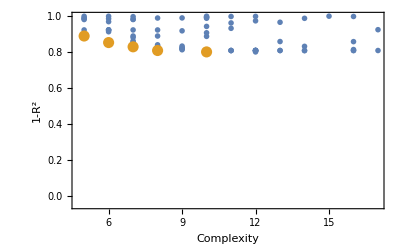

```mathematica
i=3;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

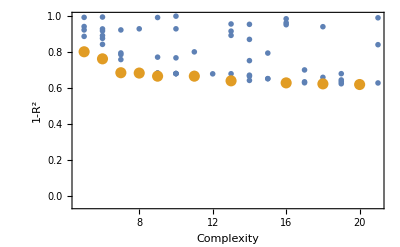

```mathematica
i=4;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

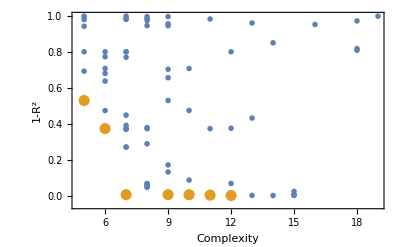

```mathematica
i=5;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

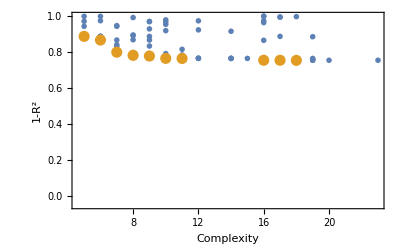

```mathematica
i=6;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

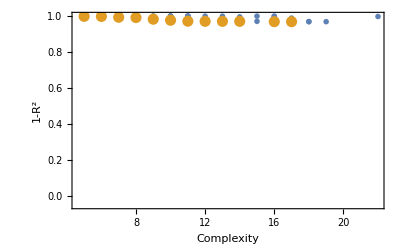

```mathematica
i=7;
r=Range[7];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

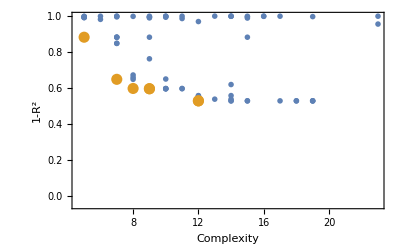

```mathematica
i=7;
r=Range[9];
PlotModels[Evolve[input[[Delete[r,i]]],input[[i]]]]
```

## Other

```mathematica
dMods=Evolve[input,response,"Ops"->Append[allOps,(Der[#1,#2]&)],"VariableNames"->{X1,X2,X3,X4,X5,X6,X7,X8,X9}];
```

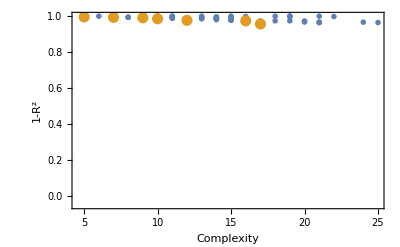

```mathematica
PlotModels[dMods]
```

```mathematica
Integrate[x,x]
```

x^2/2

```mathematica
Der[x_,y_?StringQ]:=D[x,y];
Der[x_,y_]:=0;
Der[x_,y_?NumericQ]:=0;
Der[x_,y_?SymbolQ]:=D[x,y];
```

```mathematica
SymbolQ=MatchQ[#,t_Symbol/;AtomQ[t]]&
```

MatchQ[#1,t_Symbol/;AtomQ[t]]&

```mathematica
test=%
```

StackGPModel[{X1,X1},{Inv[#1]&,ℵ1,ℵ1,√#1&,#1 #2&,ℵ1,√#1&,ℵ1,ℵ1},{},{},{},{},{},{},{X1},0]

```mathematica
test[[2]][[5]]=(Der[#1,#2]&)
```

Der[#1,#2]&

```mathematica
test
```

StackGPModel[{X1,X1},{Inv[#1]&,ℵ1,ℵ1,√#1&,Der[#1,#2]&,ℵ1,√#1&,ℵ1,ℵ1},{},{},{},{},{},{},{X1},0]

```mathematica
Symbol
```

```mathematica
test[[$VariableNames]]
```

List[X1]

```mathematica
Der[X1,2]
```

0

```mathematica
D[x*2,2]
```

General::ivar: 2 is not a valid variable.

∂_2 (2 x)

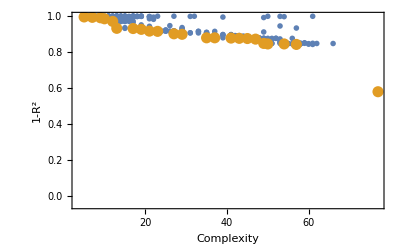

```mathematica
PlotModels[models,input,response]
```

```mathematica
goodMod1=SetModelQuality[goodMod,input,response]
```

StackGPModel[{14.6443,-7,-1,X2,2,4,X1,-1,X7,2,4,X7,-1,X2,2,4,2.71828,X1},{ℵ1,ℵ1,ℵ1,ℵ1,#1 #2&,ℵ1,Log[#1]&,ArcCos[#1]&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,ArcCos[#1]&,ℵ1,#1^#2&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,Tan[#1]&,ℵ1,#1^#2&,Log[#1]&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,#1 #2&,Sin[#1]&,Tan[#1]&,#1 #2 #3 #4 #5&,#1+#2&},{},{},{},0.579572,77,{},{X1,X2,X3,X4,X5,X6,X7,X8,X9},0]

```mathematica
AppendTo[models,goodMod1]
```

```mathematica
pFront=AdjustConstants[ParetoFrontModels[models],input,response];
```

$Aborted

```mathematica
StackGPModelAccuracy[pFront,input,response]
```

{0.853084,0.853084,0.876462,0.877429,0.877429,0.884833,0.891427,0.897328,0.906758,0.899136,0.91072,0.9153,0.916704,0.920413,0.928815,0.922619,0.935579,0.970689,0.981631,0.993257,0.995451}

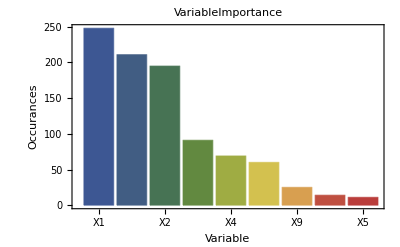

```mathematica
VariableImportancePlot[models]
```

```mathematica
goodMod=5.454925E-7*(X1 - ArcCos[Sin[X7]]^2)^4*(-X2 + ArcCos[Log[2]])^4*(X7 - Log[Tan[Sin[X2]]^2])^4*Tan[Sin[2.71828182845905*X1]] - 0.18374296231458
```

14.6443-7 (-X2+ArcCos[Log[2]])^4 (X1-ArcCos[Sin[X7]]^2)^4 (X7-Log[Tan[Sin[X2]]^2])^4 Tan[Sin[2.71828 X1]]

```mathematica
5.454925e-7*(x0-acos(sin(x6))**2)**4*(-x1+acos(log(2)))**4*(x6-log(tan(sin(x1))**2))**4*tan(sin(2.71828182845905*x0))-0.18374296231458
```

```mathematica
goodMod=ExpressionToStack[goodMod]
```

StackGPModel[{14.6443,-7,-1,X2,2,4,X1,-1,X7,2,4,X7,-1,X2,2,4,2.71828,X1},{ℵ1,ℵ1,ℵ1,ℵ1,#1 #2&,ℵ1,Log[#1]&,ArcCos[#1]&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,ArcCos[#1]&,ℵ1,#1^#2&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,Tan[#1]&,ℵ1,#1^#2&,Log[#1]&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,#1 #2&,Sin[#1]&,Tan[#1]&,#1 #2 #3 #4 #5&,#1+#2&},{},{},{},{},{},{},{},0]

```mathematica
PrintModel@goodMod
```

14.6443-7. (0.80495-1. X2)^4 (X1-1. ArcCos[Sin[X7]]^2)^4 (X7-1. Log[Tan[Sin[X2]]^2])^4 Tan[Sin[2.71828 X1]]

```mathematica
goodMod[[$VariableNames]]={X1,X2,X3,X4,X5,X6,X7,X8,X9}
```

{X1,X2,X3,X4,X5,X6,X7,X8,X9}

```mathematica
StackGPModelAccuracy[goodMod,input,response]
```

0.579572

```mathematica
goodMod/.{X1->"X1",X2->"X2",X3->"X3",X4->"X4",X5->"X5",X6->"X6",X7->"X7",X8->"X8",X9->"X9"}
```

StackGPModel[{14.6443,-7,-1,X2,2,4,X1,-1,X7,2,4,X7,-1,X2,2,4,2.71828,X1},{ℵ1,ℵ1,ℵ1,ℵ1,#1 #2&,ℵ1,Log[#1]&,ArcCos[#1]&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,ArcCos[#1]&,ℵ1,#1^#2&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,Tan[#1]&,ℵ1,#1^#2&,Log[#1]&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,#1 #2&,Sin[#1]&,Tan[#1]&,#1 #2 #3 #4 #5&,#1+#2&},{},{},{},{},{},{},{X1,X2,X3,X4,X5,X6,X7,X8,X9},0]

```mathematica
goodMod
```

StackGPModel[{14.6443,-7,-1,X2,2,4,X1,-1,X7,2,4,X7,-1,X2,2,4,2.71828,X1},{ℵ1,ℵ1,ℵ1,ℵ1,#1 #2&,ℵ1,Log[#1]&,ArcCos[#1]&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,ArcCos[#1]&,ℵ1,#1^#2&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,ℵ1,Sin[#1]&,Tan[#1]&,ℵ1,#1^#2&,Log[#1]&,#1 #2&,#1+#2&,ℵ1,#1^#2&,ℵ1,ℵ1,#1 #2&,Sin[#1]&,Tan[#1]&,#1 #2 #3 #4 #5&,#1+#2&},{},{},{},{},{},{},{X1,X2,X3,X4,X5,X6,X7,X8,X9},0]

```mathematica
PrintModel@goodMod
```

14.6443-7. (0.80495-1. X2)^4 (X1-1. ArcCos[Sin[X7]]^2)^4 (X7-1. Log[Tan[Sin[X2]]^2])^4 Tan[Sin[2.71828 X1]]